# Learning tabular data

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

```mathematica
?neurallogic`*
```

## Get data

```mathematica
data=ResourceData["663653b1-6151-48ad-b693-3ee813b191c6"]
```

Dataset[<>]

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

## Create feature encoders

```mathematica
Encoders[data_]:=Block[{
features=Normal[Keys@First[data]],
featureValues
},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->NetEncoder[{"Class",Last[#],"IndicatorVector"}]&/@featureValues]
]
encoders=Encoders[trainData];
inputSize=Total[First[#["Output"]]&/@Normal/@Values[Drop[encoders,-1]]];
classes=Normal[DeleteDuplicates[data[All,"Acceptability"]]];
```

```mathematica
featureLayer=NetGraph[
<|
"Catenate"->CatenateLayer[]
|>,
Map[NetPort[First[#]]->"Catenate"&,Drop[Normal[encoders],-1]],
"PurchasePrice"->encoders["PurchasePrice"],
"MaintenanceCost"->encoders["MaintenanceCost"],
"Doors"->encoders["Doors"],
"Passengers"->encoders["Passengers"],
"Cargo"->encoders["Cargo"],
"Safety"->encoders["Safety"]
];
```

## Create net

```mathematica
{softNet,hardNet}=Block[{numClasses=Length[classes],classificationLayerSize},
classificationLayerSize=100*numClasses;
HardNeuralChain[{
HardNeuralNAND[inputSize,classificationLayerSize],
HardNeuralNOR[classificationLayerSize,classificationLayerSize],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
net=NetGraph[<|"FeatureLayer"->featureLayer,"SoftNet"->softNet|>,{"FeatureLayer"->"SoftNet"}];
```

```mathematica
trainableNet=NetGraph[
<|"Net"->net,"Loss"->HardClassificationLoss[]|>,
{NetPort["Acceptability"]->NetPort["Loss","Target"],"Net"->"Loss"},
"Acceptability"->encoders["Acceptability"]
];
```

## Train net

```mathematica
result=NetTrain[trainableNet,trainData,All,
ValidationSet->{RandomSample[testData,UpTo[1000]],"Interval"->10},
LossFunction->"Loss",
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

## Evaluate soft net

```mathematica
trainedSoftNet=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[result["TrainedNet"]],"Loss/Error"]|>,
{},"Output"->NetDecoder[encoders["Acceptability"]]
];
```

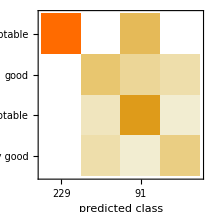
Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (91.31.5) %
Accuracy baseline | (70.22.5) %
Geometric mean of probabilities | 0.782 ± 0.031
Mean cross entropy | 0.246 ± 0.039
Single evaluation time | 3.61 ms/example
Batch evaluation speed | 1.93 examples/ms
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[trainedSoftNet,testData->"Acceptability"]
```

## Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedSoftNet];
```

```mathematica
be=HardNetBooleanExpression[hnf,inputSize];
```

```mathematica
bf=HardNetBooleanFunction[hnf,inputSize];
```

```mathematica
HardClassPrediction[m_]:=Block[{totals=Total/@N[Boole[m]]},totals/Total[totals]]
HardNetClassify[hardNet_Function,featureLayer_NetGraph,data_]:=HardClassPrediction[hardNet[Normal[featureLayer[#]]]]&/@data
HardNetClassifyWithTarget[hardNet_Function,featureLayer_NetGraph,decoder_NetDecoder,data_,targetName_String]:=[<|"Prediction"->First[decoder[HardNetClassify[hardNet,featureLayer,{KeyDrop[{targetName}]@#}]]],"Target"->#[targetName]|>&,data]
HardNetClassifyEvaluation[hardNetClassifyTargetPairs_]:=Module[
{counts=Counts[hardNetClassifyTargetPairs],correctExamples,accuracy},
correctExamples=Select[Normal[counts],With[{assoc=First[#]},Length[DeleteDuplicates[Values[assoc]]]]==1&];
accuracy=N[Total[Last/@correctExamples]/Total[counts]];
<|"Accuracy"->accuracy|>
]
```

```mathematica
hncwt=HardNetClassifyWithTarget[bf,featureLayer,NetDecoder[encoders["Acceptability"]],testData,"Acceptability"];
```

```mathematica
eval=HardNetClassifyEvaluation[hncwt]
```

<|Accuracy→0.913295|>